```mathematica
Quit[]
```

```mathematica
NotebookDirectory[]
```

/home/riccardo/Documents/Fisica/Tesi/Processes/diagrams/qqmm1L/

## Input

```mathematica
<<"/home/riccardo/Programs/ABISS/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

```mathematica
SetPath[NotebookDirectory[]];
process={F[3,{1,o}],-F[3,{1,o}]}->{F[2,{2}],-F[2,{2}]};
SetProcess[process];
```

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/Processes/diagrams/qqmm1L/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/Processes/diagrams/qqmm1L/input/integral_families.m already exist. It will NOT be overwritten.

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/diagrams/qqmm1L/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/diagrams/qqmm1L/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/diagrams/qqmm1L/input/equivalence_classes.m

## Functions

```mathematica
fields1Lperm=<<(NotebookDirectory[]<>"backup/fields/fields1Lperm.m");
```

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
chargeReplace={Ql->-1,I3l->-1/2,I3N->1/2,Qu->2/3,I3u->1/2,Qd->-1/3,I3d->-1/2};
cwReplace={cw->Sqrt[1-sw^2],mw->mz Sqrt[1-sw^2]};
```

```mathematica
notNull[x_]:=Module[{result},
If[x===0,result=0,result=1];
Return[result]
]
contributions[coefflist_List]:=Module[{result},
If[MatrixQ[coefflist],
result=Map[notNull,coefflist,{2}];
Return[result]
,
Message[contributions::nomatrix,"Argument is not a matrix"];
Return[Null]
]
]

notNullElements[ll_List]:=Module[{result},
result={};
Do[
If[ll[[i]]=!=0,result=AppendTo[result,i]]
,{i,Length[ll]}];
Return[result]
]
```

```mathematica
masters=<<(NotebookDirectory[]<>"final_results/Masters.m");
diagramCoefficients=<<(NotebookDirectory[]<>"final_results/diagramCoefficients.m");
diagramRepCoefficients=<<(NotebookDirectory[]<>"final_results/diagramRepCoefficients.m");
timeCoefficients=<<(NotebookDirectory[]<>"final_results/diagramTime.m");
totalCoefficients=<<(NotebookDirectory[]<>"final_results/totalCoefficients.m");
```

```mathematica
xiMasters={};
xiMastersW={};
xiMastersZ={};
Do[
If[!FreeQ[masters[[i]],GaugeXi[_]],
xiMasters=AppendTo[xiMasters,i];
If[!FreeQ[Cases[masters[[i]],mz*Sqrt[GaugeXi[_]],Infinity],mz],
xiMastersZ=AppendTo[xiMastersZ,i]
];
If[!FreeQ[Cases[masters[[i]],mw*Sqrt[GaugeXi[_]],Infinity],mw],
xiMastersw=AppendTo[xiMastersW,i]
]
]
,{i,Length[masters]}]
```

## Contributions

```mathematica
Print["Numero totale di Master:  ", Length[masters]];
```

Numero totale di Master:  50

```mathematica
Print["Numero totale di Master dipendenti da xi:  ", Length[xiMasters]]
```

Numero totale di Master dipendenti da xi:  15

```mathematica
contr=contributions[diagramRepCoefficients];
```

I seguenti master integral dipendenti da xi hanno dei coefficienti non nulli. Alcuni di questi master integral non sono effetivamente indipendenti tra loro. Ma anche individuando i master che coincidono, comunque il coefficiente totale è non nullo.

```mathematica
xiMastersCoeffs=Map[totalCoefficients[[#]]&,xiMasters];
Do[
If[xiMastersCoeffs[[i]]=!=0,Print[xiMasters[[i]], ":  " , masters[[xiMasters[[i]]]]]]
,{i,Length[xiMastersCoeffs]}]
```

9:  userIntegral[A7,{mz √GaugeXi[Q]},1,0,0,0]

23:  userIntegral[A5,{mw,mw √GaugeXi[Q]},0,0,1,0]

24:  userIntegral[A5,{mw,mw √GaugeXi[Q]},0,1,1,0]

26:  userIntegral[A5,{mw √GaugeXi[Q],mw},0,0,1,0]

27:  userIntegral[A5,{mw √GaugeXi[Q],mw},0,1,1,0]

28:  userIntegral[A7,{mw √GaugeXi[Q]},1,0,0,0]

29:  userIntegral[A4,{mw √GaugeXi[Q]},0,1,1,0]

Di seguito c' è un breve codice per mostrare quali diagrammi contribuiscono a questi master integral (l' indce n indica il numero del master preso in considerazione.In questo caso guardiamo il primo master dipendente da xi con coefficiente non nullo, cioè n = 9)

```mathematica
n=29;
m=masters[[n]];
Print["Master:  ",m];
Print["Momenta:  ", userPropagatorMomenta[m[[1]]]];
Print["Masses:  ", userIntegralMasses[m[[1]]]];
```

Master:  userIntegral[A4,{mw √xi_Q},0,1,1,0]

Momenta:  {q1,-p1+q1,p2+q1,-p1+p3+q1}

Masses:  {0,M1,M1,0}

> Top. 1 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 2 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 3 aebf/cgdg/ghefehfh.m, 0 diagrams

> Top. 4 aebe/cfdf/egfhghgh.m, 0 diagrams

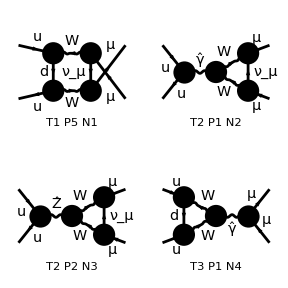

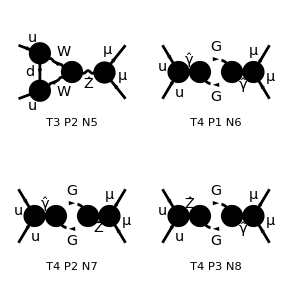

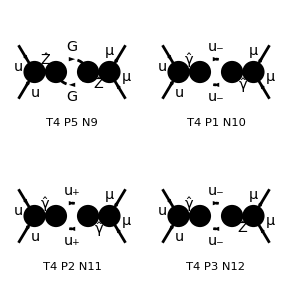

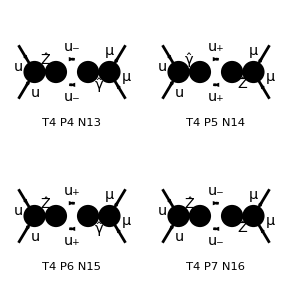

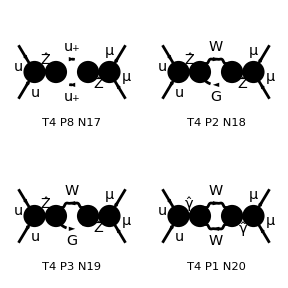

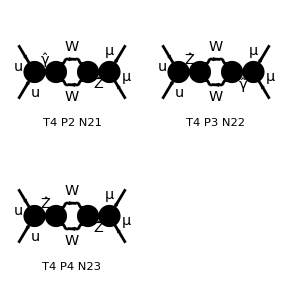

```mathematica
diagramList=notNullElements[Transpose[diagramRepCoefficients][[n]]];
Paint[DiagramExtract[fields1Lperm,diagramList],ColumnsXRows->2];
```